# Práctica II

Carlos Santiago Galindo Jiménez
Sergio Alemany Ibor

## Práctica 2.1 - Simular un autómata celular unidimensional

```mathematica
IntToRegla[num_Integer]:=Module[{res, i,n},
res = {};
i=0;
n=num;
While[i<8,
AppendTo[res,{Mod[Quotient[i,4],2],Mod[Quotient[i,2],2],Mod[i,2],Mod[n,2]}];
n=Quotient[n,2];
i++;
];
Return[res];
];
ACItera[inicial_List,regla_List]:=Module[{final,i},
final={};
For[i=1,i≤Length[inicial],i++,
AppendTo[final,Cases[regla,{inicial[[Mod[i-2,Length[inicial]]+1]],inicial[[i]],inicial[[Mod[i,Length[inicial]]+1]],_}][[1,4]]];
];
Return[final];
];
AC[Inicial_List,transicion_List,t_Integer]:=Module[{res,i},
res={Inicial};
For[i=1,i≤t+1,i++,
AppendTo[res,ACItera[res[[i]],transicion]];
];
Return[res];
];
```

```mathematica
ArrayPlot[AC[{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0},IntToRegla[150],25]]
```

## Práctica 2.2 - Autómatas finitos como autómatas celulares

Un autómata es una lista con {Q,∑,δ,q_0,F}, donde Q es una lista de estados, F es un subconjunto de Q representando los estados finales, q_0 es el estado inicial y ∑ es el alfabeto del autómata. δ es una lista de transiciones con la siguiente forma {q,a,q’} donde q, q’ ∈ ∑ y a ∈ ∑, siendo q el estado actual, a la letra generada y q’ el estado de destino.

### Ejercicio 1 - Convertir AFD a AC unidireccional unidimensional con entrada paralela

```mathematica
AFDToCellularAutomata[afd_List]:=Module[{S,Sp,f,i,j,c},
S=afd[[1]]∪afd[[2]];
Sp=afd[[5]];
f=afd[[3]];
(*Insertar transiciones {q,q',q'} ∀ q,q' ∈ Q*)
(*Insertar transiciones {a,a',a'} ∀ a,a' ∈ ∑*)
For[c=1,c≤2,c++,
For[i=1,i≤Length[afd[[c]]],i++,
For[j=1,j≤Length[afd[[c]]],j++,
AppendTo[f,{afd[[c,i]],afd[[c,j]],afd[[c,j]]}];
];
];
];
Return[{S,f,Sp}];
];
afd1={{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}};
```

```mathematica
AC=AFDToCellularAutomata[afd1]
```

{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}

### Ejercicio 2 - Comprobar si una cadena es aceptada por un AC unidimensional y de entrada paralela en tiempo real, indicando el estado de frontera q ∈ S

```mathematica
ACcheckCadena[cadena_List,AC_List,frontera_]:=Module[{res,i,j,aux},
res=cadena;
For[i=1,i≤Length[res],i++,
aux={Cases[AC[[2]],{frontera,res[[1]],_}][[1,3]]};
For[j=2,j≤Length[res],j++,
AppendTo[aux,Cases[AC[[2]],{res[[j-1]],res[[j]],_}][[1,3]]];
];
res=aux;
];
Return[MemberQ[AC[[3]],res[[Length[cadena]]]]];
];
AC1=AFDToCellularAutomata[afd1];
```

```mathematica
ACcheckCadena[{a,b,a,a,b},AC,q]
```

True

### Ejercicio 3 - a partir de un AFD generar un AC equivalente unidimensional bidireccional

```mathematica
AFDToCellularAutomata2[afd_List]:=Module[{res,f,i,j},
res=AFDToCellularAutomata[afd];
(*Convert all transitions {a,b,c} to transitions {a,b,x,c}, ∀x∈S*)
f={};
For[i=1,i≤Length[res[[2]]],i++,
For[j=1,j≤Length[res[[1]]],j++,
AppendTo[f,{res[[2,i,1]],res[[2,i,2]],res[[1,j]],res[[2,i,3]]}];
];
];
res[[2]]=f;
Return[res];
];
```

```mathematica
AFDToCellularAutomata2[afd1]
```

{{a,b,p,q,r},{{q,a,a,p},{q,a,b,p},{q,a,p,p},{q,a,q,p},{q,a,r,p},{q,b,a,r},{q,b,b,r},{q,b,p,r},{q,b,q,r},{q,b,r,r},{p,a,a,r},{p,a,b,r},{p,a,p,r},{p,a,q,r},{p,a,r,r},{p,b,a,q},{p,b,b,q},{p,b,p,q},{p,b,q,q},{p,b,r,q},{r,a,a,r},{r,a,b,r},{r,a,p,r},{r,a,q,r},{r,a,r,r},{r,b,a,r},{r,b,b,r},{r,b,p,r},{r,b,q,r},{r,b,r,r},{q,q,a,q},{q,q,b,q},{q,q,p,q},{q,q,q,q},{q,q,r,q},{q,p,a,p},{q,p,b,p},{q,p,p,p},{q,p,q,p},{q,p,r,p},{q,r,a,r},{q,r,b,r},{q,r,p,r},{q,r,q,r},{q,r,r,r},{p,q,a,q},{p,q,b,q},{p,q,p,q},{p,q,q,q},{p,q,r,q},{p,p,a,p},{p,p,b,p},{p,p,p,p},{p,p,q,p},{p,p,r,p},{p,r,a,r},{p,r,b,r},{p,r,p,r},{p,r,q,r},{p,r,r,r},{r,q,a,q},{r,q,b,q},{r,q,p,q},{r,q,q,q},{r,q,r,q},{r,p,a,p},{r,p,b,p},{r,p,p,p},{r,p,q,p},{r,p,r,p},{r,r,a,r},{r,r,b,r},{r,r,p,r},{r,r,q,r},{r,r,r,r},{a,a,a,a},{a,a,b,a},{a,a,p,a},{a,a,q,a},{a,a,r,a},{a,b,a,b},{a,b,b,b},{a,b,p,b},{a,b,q,b},{a,b,r,b},{b,a,a,a},{b,a,b,a},{b,a,p,a},{b,a,q,a},{b,a,r,a},{b,b,a,b},{b,b,b,b},{b,b,p,b},{b,b,q,b},{b,b,r,b}},{r}}

### Ejercicio 4 - Mostrar la secuencia de computación de la actividad 2 en un diagrama espacio - temporal

```mathematica
ACcheckCadenaHistorial[cadena_List,AC_List,frontera_]:=Module[{res,i,j,aux},
res={cadena};
For[i=1,i≤Length[cadena],i++,
aux={Cases[AC[[2]],{frontera,res[[1,1]],_}][[1,3]]};
For[j=2,j≤Length[res[[1]]],j++,
AppendTo[aux,Cases[AC[[2]],{res[[1,j-1]],res[[1,j]],_}][[1,3]]];
];
PrependTo[res,aux];
];
Return[res];
];
(*Este metodo no funciona, da error en las transiciones*)
ACHistorialFromAFD[cadena_List,AFD_List]:=Module[{ACaux,list},
ACaux=AFDToCellularAutomata2[AFD];
list=cadena;
PrependTo[list,AFD[[4]]];
AppendTo[list,AFD[[4]]];
Return[AC[list,ACaux[[2]],Length[list]]];
];
```

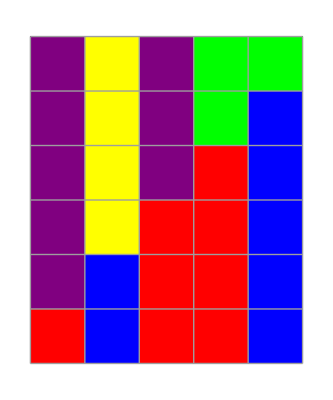

```mathematica
ArrayPlot[ACcheckCadenaHistorial[{a,b,a,a,b},AC1,q],ColorRules->{a->Red,b->Blue,q->Yellow,p->Purple,r->Green},Mesh->True]
```